# Local Optimization on the Gaussian manifold

This notebook is intended as a guide to using the optimization algorithm performing gradient descent over the manifold of pure bosonic or fermionic Gaussian states.

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<GaussianOptimization`
```

# The GaussianOptimization.m package and its functions

All functions included in the package, in alphabetical order:

```mathematica
?"GaussianOptimization`*"
```

## Optimization algorithm

```mathematica
?GOOptimize
```

The function GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific] provides a general gradient descent optimization algorithm and sits at the core of the GO package.

{FinalF,FinalM,CorrList,FinalFlist,Flists,FinalNormlist}=GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]

The input consists of the following pieces:
ProblemSpecific={F,dF}
	F represents the function to be minimized
	dF represents the gradient function of f
SystemSpecific={J0,listM0,KK,geometry,newM}
	J0 represents a reference point
	listM0 represents a list of starting points, i.e., of transformations from the reference point J0
	KK represents a local basis of tangent space (e.g. subspace of Lie algebra)
	geometry represents a local notion of geometry (e.g. metric) with respect to KK
	newM represents the function that takes the gradient as input and constructs a new point on the state manifold
ProcedureSpecific={tolF,tolgrad,steplimit,stepsizefunction,trackall}
	tolF represents the stopping tolerance of the function value of F
	tolgrad represents the stopping tolerance of the gradient norm of dF
	steplimit represents a maximal number of steps (typically, we choose ∞)
	trackall is an option to track all trajectories starting from listM0 instead of dropping some

The output consists of the following pieces:
{FinalF,FinalM,CorrList,FinalFlist,Flists,FinalNormlist}
	FinalF represents the final function value of F
	FinalM represents the final transformation from J0 to the final state
	CorrList lists the number of stepsize corrections at each step of the final trajectory
	FinalFlists lists the successive function values in the optimal trajectory
	Flists lists all successive function values for all trajectories (Lucas: is that right?)
	FinalNormlist lists the successive gradient norms in the optimal trajectory

For a more detailed explanation of the input arguments, see the guide to setting up a customization at the end of this document!

## Basic Tools and Fundamental definitions

Symplectic forms and Covariance matrices

For Bosonic states

```mathematica
?GOΩqpqp
```

GOΩqpqp[N] generates Ω in basis (q_1,p_1,q_2,p_2,...) for N deg. of freedom

```mathematica
?GOΩqqpp
```

GOΩqqpp[N] generates Ω in basis (q_1,q_2,...,p_1,p_2,...) for N deg. of freedom

```mathematica
?GOΩaabb
```

GOΩaabb[N] generates Ω in basis (a_1,a_2,...,b_1,b_2,...) for N deg. of freedom

```mathematica
?GOΩabab
```

GOΩabab[N] generates Ω in basis (a_1,b_1,a_2,b_2,...) for N deg. of freedom

For Fermionic states

```mathematica
?GOGqpqp
```

GOGqpqp[N] generates G in basis (q_1,p_1,q_2,p_2,...) for N deg. of freedom

```mathematica
?GOGqqpp
```

GOGqqpp[N] generates G in basis (q_1,q_2,...,p_1,p_2,...) for N deg. of freedom

```mathematica
?GOGaabb
```

GOGaabb[N] generates G in basis (a_1,a_2,...,b_1,b_2,...) for N deg. of freedom

```mathematica
?GOGabab
```

GOGabab[N] generates G in basis (a_1,b_1,a_2,b_2,...) for N deg. of freedom

Transforming between structures

```mathematica
?GOTransformGtoJ
```

GOTransformGtoJ[G,'Gbasis','Jbasis'] generates J in Jbasis associated with G in Gbasis

```mathematica
?GOTransformΩtoJ
```

GOTransformΩtoJ[Ω,'Ωbasis','Jbasis'] generates J in Jbasis associated with Ω in Ωbasis

```mathematica
?GOTransformJtoG
```

GOTransformJtoG[J,'Jbasis','Gbasis'] generates G in Gbasis associated with J in Jbasis

```mathematica
?GOTransformJtoΩ
```

GOTransformJtoΩ[J,'Jbasis','Ωbasis'] generates Ω in Ωbasis associated with J in Jbasis

Basis Transformation matrices

We provide basis transformation matrices for transformations between four bases (note that b_i are the respective annihilation operators):
 (q_1,p_1,q_2,p_2,...) 	(q_1,q_2,...,p_1,p_2,...)	(a_1,b_1,a_2,b_2,...)	(a_1,a_2,...,b_1,b_2,...)

where we have defined:		a_i=1/(√2)(q_i+ⅈ p_i)  and   b_i=1/(√2)(q_i-ⅈ p_i)

Re-ordering

```mathematica
?GOqqppFROMqpqp
```

GOqqppFROMqpqp[N] generates a basis transformation (q_1,p_1,q_2,p_2,...)→(q_1,q_2,...,p_1,p_2,...) for N deg. of freedom

```mathematica
?GOqpqpFROMqqpp
```

GOqpqpFROMqqpp[N] generates a basis transformation (q_1,q_2,...,p_1,p_2,...)→(q_1,p_1,q_2,p_2,...) for N deg. of freedom

```mathematica
?GOaabbFROMabab
```

GOaabbFROMabab[N] generates a basis transformation (a_1,b_1,a_2,b_2,...)→(a_1,a_2,...,b_1,b_2,...) for N deg. of freedom

```mathematica
?GOababFROMaabb
```

GOababFROMaabb[N] generates a basis transformation (a_1,a_2,...,b_1,b_2,...)→(a_1,b_1,a_2,b_2,...) for N deg. of freedom

position / momentum → annihilation / creation operators

```mathematica
?GOababFROMqpqp
```

GOababFROMqpqp[N] generates a basis transformation (q_1,p_1,q_2,p_2,...)→(a_1,b_1,a_2,b_2,...) for N deg. of freedom

```mathematica
?GOaabbFROMqpqp
```

GOaabbFROMqpqp[N] generates a basis transformation (q_1,p_1,q_2,p_2,...)→(a_1,a_2,...,b_1,b_2,...) for N deg. of freedom

```mathematica
?GOababFROMqqpp
```

GOababFROMqqpp[N] generates a basis transformation (q_1,q_2,...,p_1,p_2,...)→(a_1,b_1,a_2,b_2,...) for N deg. of freedom

```mathematica
?GOaabbFROMqqpp
```

GOaabbFROMqqpp[N] generates a basis transformation (q_1,q_2,...,p_1,p_2,...)→(a_1,a_2,...,b_1,b_2,...) for N deg. of freedom

annihilation / creation operators → position / momentum

```mathematica
?GOqpqpFROMabab
```

GOqpqpFROMabab[N] generates a basis transformation (a_1,b_1,a_2,b_2,...)→(q_1,p_1,q_2,p_2,...) for N deg. of freedom

```mathematica
?GOqqppFROMabab
```

GOqqppFROMabab[N] generates a basis transformation (a_1,b_1,a_2,b_2,...)→(q_1,q_2,...,p_1,p_2,...) for N deg. of freedom

```mathematica
?GOqpqpFROMaabb
```

GOqpqpFROMaabb[N] generates a basis transformation (a_1,a_2,...,b_1,b_2,...)→(q_1,p_1,q_2,p_2,...) for N deg. of freedom

```mathematica
?GOqqppFROMaabb
```

GOqqppFROMaabb[N] generates a basis transformation (a_1,a_2,...,b_1,b_2,...)→(q_1,q_2,...,p_1,p_2,...) for N deg. of freedom

Lie algebra bases

All Lie algebra bases are generated in the basis  (q_1,p_1,q_2,p_2,...)  by convention

```mathematica
?GOLieBasisSp
GOLieBasisSp[2]//Dimensions
```

GOLieBasisSp[N] generates Sp(2N,R) Lie algebra basis in basis (q_1,p_1,q_2,p_2,...)

{10,4,4}

```mathematica
?GOLieBasisSpNoUN
GOLieBasisSpNoUN[2]//Dimensions
```

GOLieBasisSpNoUN[N] generates Sp(2N,R)/U(N) Lie algebra basis in basis (q_1,p_1,q_2,p_2,...)

{6,4,4}

```mathematica
?GOLieBasisSpNoU1
```

GOLieBasisSpNoU1[N] generates Sp(2N,R)/U(1)^N Lie algebra basis in basis (q_1,p_1,q_2,p_2,...)

```mathematica
?GOLieBasisSpMixing
GOLieBasisSpMixing[1,1]//Dimensions
```

GOLieBasisSpMixing[N_A,N_B] generates the compound Lie algebra basis sp(2(N_A+N_B),R)/sp(2N_A,R) x sp(2N_B,R)

{4,4,4}

```mathematica
?GOLieBasisSO
GOLieBasisSO[2]//Dimensions
```

GOLieBasisSO[N] generates O(2N,R) Lie algebra basis in basis (q_1,p_1,q_2,p_2,...)

{6,4,4}

```mathematica
?GOLieBasisSONoUN
```

GOLieBasisSpNoUN[N] generates SO(2N,R)/U(N) Lie algebra basis in basis (q_1,p_1,q_2,p_2,...)

```mathematica
?GOLieBasisEmpty
GOLieBasisEmpty[2]//Dimensions
```

GOLieBasisEmpty[N] constructs the empty Lie basis given by a list containing a single 2N by 2N matrix with zero entries. It can be used to construct a compound basis using GOLieBasisCompound.

{1,4,4}

We can also construct a compound Lie algebra basis for a system that is divided into two subsystems:

```mathematica
?GOLieBasisCompound
GOLieBasisCompound[{GOLieBasisEmpty[2],GOLieBasisSp[2],GOLieBasisEmpty[6]}]//Dimensions
```

GOCompoundBasis[{LieAlgebra1,LieAlgebra2,...,LieAlgebraN}] creates the space spanned by different Lie algebra spaces collected in a vector {LieAlgebra1,LieAlgebra2,...,LieAlgebraN}. For degrees of freedom without changes, we should include GOLieAlgebraEmpty[n].

{10,20,20}

Metrics for the symplectic and orthogonal manifolds

```mathematica
?GOMetricSp
```

GOMetricSp[K,J_0] generates the natural metric for the symplectic manifold with Lie basis K, for an initial state J_0

```mathematica
?GOMetricO
```

GOMetricO[K,J_0] generates the natural metric for the orthogonal manifold with Lie basis K

```mathematica
?GOGeometryConst
```

GeometryConst[LieBasis,J0,pm] creates the list geometry={metric,invmetric} of a constant geometry around J0. It works for both, bosonic and fermionic systems by choosing pm=+1 for bosons and pm=-1 for fermions.

Generating random Transformations

```mathematica
?GORandomTransformation
```

GORandomTransformation[n,'Basis'] generates a random transformation in the Lie group with algebra 'Basis'

Tools for computational efficiency

```mathematica
?GOapproxExp
```

GOapproxExp[ϵ,K]=(1 + ϵ/2 K)/(1 - ϵ/2 K) approximates MatrixExponential[ϵX]

```mathematica
?GOlogfunction
```

GOlogfunction[x] takes value 0 when x=0 and log[x] otherwise

```mathematica
?GOConditionalLog
```

GOConditionalLog[x] calculates MatrixLog[x] by applying logfunction to the eigenvalues of x

```mathematica
?GOinvMSp
```

GOinvMSp[m,'Mform'] inverts a symplectic matrix m in the basis Mform as m^-1=-ΩmΩ

## Applications implemented in GaussianOptimization.m

Purifications and the standard form

```mathematica
?GOExtractStdFormG
```

{rlist,Tra}=GOExtractStdFormG[G]
Returns the parameters for constructing the standard form of G (list of the r_i and the transformation matrix Tra that puts G into standard form

```mathematica
?GOExtractStdFormΩ
```

{rlist,Tra}=GOExtractStdFormΩ[Ω]
Returns the parameters for constructing the standard form of Ω (list of the r_i and the transformation matrix Tra that puts Ω into standard form

```mathematica
?GOPurifyStandardGBoson
```

G_sta=GOPurifyStandardGBoson[rlist,N,'Gform']
Constructs the bosonic purified state convariance matrix in the basis Gform with N degrees of freedom in the ancillary

```mathematica
?GOPurifyStandardJBoson
```

J_sta=GOPurifyStandardJBoson[rlist,N,'Jform']
Constructs the bosonic purified state complex structure in the basis Jform with N degrees of freedom in the ancillary

```mathematica
?GOPurifyStandardΩFermion
```

Ω_sta=GOPurifyStandardΩFermion[rlist,N,'Ωform']
Constructs the fermionic purified state convariance matrix in the basis Ωform with N degrees of freedom in the ancillary

```mathematica
?GOPurifyStandardJFermion
```

J_sta=GOPurifyStandardJFermion[rlist,N,'Jform']
Constructs the fermionic purified state complex structure in the basis Jform with N degrees of freedom in the ancillary

Entanglement of Purification

```mathematica
?GORestrictionAA
```

GORestrictionAA[{dimA1, dimB1, dimA2, dimB2}] generates the restriction function for use in calculating EoP for a system decomposed into degrees of freedom {dimA1, dimB1, dimA2, dimB2}

```mathematica
?GOEoPBos
```

GOEoPBos[Restriction] generates a function f[M,J_0] which calculates the bosonic EoP for the given restriction

```mathematica
?GOEoPgradBos
```

GOEoPgradBos[Restriction] generates a function df[M,J_0,K,G^-1] which calculates the gradient of the bosonic EoP for the given restriction with respect to the Lie algebra basis K

```mathematica
?GOEoPFerm
```

GOEoPBos[Restriction] generates a function f[M,J_0] which calculates the fermionic EoP for the given restriction

```mathematica
?GOEoPgradFerm
```

GOEoPgradFerm[Restriction] generates a function df[M,J_0,K,G^-1] which calculates the gradient of the fermionic EoP for the given restriction with respect to the Lie algebra basis K

Complexity of Purification

```mathematica
?GOCoPBos
```

GOCoPBos[J_T] generates a function f[M,J_R0] which calculates the bosonic CoP with respect to the given target state J_T

```mathematica
?GOCoPgradBos
```

GOCoPBos[J_T] generates a function df[M,J_R0,K,G^-1] which calculates the gradient of the bosonic CoP with respect to the given target state J_T and the Lie algebra basis K

```mathematica
?GOCoPFerm
```

GOCoPFerm[J_T] generates a function f[M,J_R0] which calculates the fermionic CoP with respect to the given target state J_T

```mathematica
?GOCoPgradFerm
```

GOCoPgradFerm[J_T] generates a function df[M,J_R0,K,G^-1] which calculates the gradient of the fermionic CoP with respect to the given target state J_T and the Lie algebra basis K

Energy of quadratic Hamiltonians

```mathematica
?GOenergyBos
```

GOenergyBos[h] generates an energy function f[M,J_0] for a bosonic quadratic Hamiltonian H=h_abξ^aξ^b

```mathematica
?GOenergygradBos
```

GOenergygradBos[h] generates an energy gradient function df[M,J_0,K] for a bosonic quadratic Hamiltonian H=h_abξ^aξ^b with respect to the Lie algebra basis K

```mathematica
?GOenergyFerm
```

GOenergyFerm[h] generates an energy function f[M,J_0] for a fermionic quadratic Hamiltonian H=h_abξ^aξ^b

```mathematica
?GOenergygradFerm
```

GOenergygradBos[h] generates an energy gradient function df[M,J_0,K] for a fermionic quadratic Hamiltonian H=h_abξ^aξ^b with respect to the Lie algebra basis K

# Selected examples: EoP and CoP

## EXECUTE FIRST: Ground state covariances matrices of Klein-Gordon field and XY model

#### Covariance matrix of ground state of the discretized Klein-Gordon field

```mathematica
KGft[{L_,l_,m_}]:=KGft[{L,l,m}]={Fourier[Table[√((m^2+(2/l Sin[(π k)/L])^2)/L),{k,0,L-1}]]//Re,Fourier[Table[1/√(L(m^2+(2/l Sin[(π k)/L])^2)),{k,0,L-1}]]//Re};
KGb[var_]:=KGb[var]={ToeplitzMatrix[KGft[var]⟦1⟧],ToeplitzMatrix[KGft[var]⟦2⟧]};
KGcm[var_]:=KGcm[var]=ArrayFlatten[{{KGb[var]⟦1⟧,0.},{0.,KGb[var]⟦2⟧}}];(* in qqpp basis *)
KGcmRes[Llm_,{dimA_,dimB_,d_}]:=KGcmRes[Llm,{dimA,dimB,d}]=Module[{ind},
ind=Join[Table[i,{i,dimA}],Table[i+dimA+d,{i,dimB}]];
GOqpqpFROMqqpp[dimA+dimB].ArrayFlatten[{{KGb[Llm]⟦1,ind,ind⟧,0.},{0.,KGb[Llm]⟦2,ind,ind⟧}}].Transpose[GOqpqpFROMqqpp[dimA+dimB]]
](* in qpqp basis *)
```

#### Covariance matrix of ground state of the XY model

```mathematica
Clear[XYft,XYcm,XYcmRes]
XYft[{L_,J_,h_,γ_}]:=XYft[{L,J,h,γ}]=Module[{ϵ,a,b,u,v,cor,part1,part2},
u[0]=0;v[0]=ⅈ;u[π]=1;v[π]=0; (* This is no really needed for even number of excitations, but would be relevant, if we were to construct eigenstates with odd number of excitations! *)
ϵ[k_]:=ϵ[k]=√(h^2+2h J Cos[k]+J^2+(γ^2-1)J^2 Sin[k]^2);
a[k_]:=a[k]=-J Cos[k]-h;
b[k_]:=b[k]=γ J Sin[k];
u[k_]:=u[k]=(ϵ[k]+a[k])/(√(2ϵ[k](ϵ[k]+a[k])));
v[k_]:=v[k]=(ⅈ b[k])/(√(2ϵ[k](ϵ[k]+a[k])));
cor=Table[ⅇ^(ⅈ π (x+1)/L),{x,0,L-1}]//N;
part1=((Table[1/(√L)(Abs[v[(2π k+π)/L]]^2-Abs[u[(2π k+π)/L]]^2//N)ⅇ^(ⅈ 2π k/L),{k,0,L-1}]//Fourier)*cor)//Re;
part2=(((Table[1/(√L)2Im[v[(2π k+π)/L]u[(2π k+π)/L]] ⅇ^(ⅈ 2π k/L),{k,0,L-1}]//Fourier)*cor)//Im);
part1+part2]

XYcm[var_]:=XYcm[var]=Module[{L,ft,ΩBlock},
L=var⟦1⟧;
ft=XYft[var];
ΩBlock=ToeplitzMatrix[ReplacePart[RotateRight[ft,1],1->-Last[ft]],-Reverse[ft]];
ArrayFlatten[{{0.,ΩBlock},{-Transpose[ΩBlock],0.}}]
](* in qqpp basis *)
XYcmRes[var_,{dimA_,dimB_,d_}]:=Module[{L,ind,ΩRes},
L=var⟦1⟧;
ind=Join[Table[i,{i,dimA}],Table[i+dimA+d,{i,dimB}]];
ΩRes=Table[If[Mod[j-l,L]==0,-Reverse[XYft[var]]⟦1⟧,Sign[j-l]XYft[var]⟦Mod[j-l,L]⟧],{j,ind},{l,ind}];
GOqpqpFROMqqpp[dimA+dimB].ArrayFlatten[{{0.,ΩRes},{-Transpose[ΩRes],0.}}].Transpose[GOqpqpFROMqqpp[dimA+dimB]]
] (* in qpqp basis *)
```

## Bosonic Entanglement of Purification (EoP)

```mathematica
L=100; (* number of lattice sites *)
l=1.; (* lattice spacing *)
m=.1; (* mass *)
dimA1=1; (* sites of subsystem A1 *)
dimB1=3; (* sites of subsystem B1 *)
d=5; (* distance between subsystem A1 and B1 *)
dimA2=dimA1+1; (* dimension of purifying subsystem A2 *)
dimB2=dimB1; (* dimension of purifying subsystem B2 *)
```

### Pre-algorithm: Create complex structures and initial transformations

```mathematica
CM0=KGcmRes[{L,l,m},{dimA1,dimB1,d}];
{rlist,MTra}=GOExtractStdFormG[CM0];
```

```mathematica
Length[rlist]
dimA2+dimB2
```

4

5

```mathematica
J0=GOPurifyStandardJBoson[rlist,dimA2+dimB2,"qpqp"];
M0=ArrayFlatten[{{Inverse[MTra],0},{0,IdentityMatrix[2dimA2+2dimB2]}}]//SparseArray;
```

#### Consistency checks

```mathematica
J0.J0//Eigenvalues (*check J0 to describe pure bosonic state*)
```

{-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.}

```mathematica
MTra.CM0.Transpose[MTra]//Chop//MatrixForm (* check correct transformation *)
Cosh[2rlist]
```

(1.46243 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.46243 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.22221 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.22221 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.06604 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.06604 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.00032 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00032)

{1.46243,1.22221,1.06604,1.00032}

```mathematica
MTra.GOinvMSp[MTra]//Chop//MatrixForm (* check symplectic *)
```

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

```mathematica
rrlist={rlist⟦1⟧,rlist⟦2⟧,rlist⟦4⟧,rlist⟦3⟧}
CMback=Inverse[MTra].DiagonalMatrix[Cosh/@Flatten[Table[{2r,2r},{r,rlist}]]].Transpose[Inverse[MTra]];CMback//MatrixForm
CM0-CMback//Chop//MatrixForm
```

{0.464018,0.327439,0.0126183,0.180728}

(1.28101 | -5.65113×10^-16 | -0.00697557 | 2.62811×10^-16 | -0.0048107 | -6.89553×10^-16 | -0.00344953 | 2.76688×10^-16
-4.54064×10^-16 | 1.39418 | -1.98192×10^-16 | 0.247118 | 8.43076×10^-16 | 0.209989 | -6.17562×10^-16 | 0.179771
-0.00697557 | -1.84314×10^-16 | 1.28101 | 1.61676×10^-15 | -0.41982 | 3.55271×10^-15 | -0.0813337 | -1.65146×10^-15
2.62811×10^-16 | 0.247118 | 1.67227×10^-15 | 1.39418 | -3.26128×10^-15 | 0.760649 | 1.22125×10^-15 | 0.554542
-0.0048107 | 8.43076×10^-16 | -0.41982 | -3.26128×10^-15 | 1.28101 | -3.33067×10^-16 | -0.41982 | 2.55351×10^-15
-6.89553×10^-16 | 0.209989 | 3.58047×10^-15 | 0.760649 | -3.33067×10^-16 | 1.39418 | -2.52576×10^-15 | 0.760649
-0.00344953 | -5.62484×10^-16 | -0.0813337 | 1.17267×10^-15 | -0.41982 | -2.55351×10^-15 | 1.28101 | -5.68989×10^-16
2.76905×10^-16 | 0.179771 | -1.70697×10^-15 | 0.554542 | 2.53964×10^-15 | 0.760649 | -6.52256×10^-16 | 1.39418)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### 1. Define the problem-specific input arguments

```mathematica
Restriction=GORestrictionAA[{dimA1,dimB1,dimA2,dimB2}];
function=GOEoPBos[Restriction];
gradient=GOEoPgradBos[Restriction];
ProblemSpecific={function,gradient};
```

### 2. Define the system-specific input arguments

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSp[dimA2+dimB2]}];
M0List=Table[MatrixExp[RandomReal[{0,0.8},Length[LieBasis]].LieBasis].M0,{i,100}];
geometry=GOGeometryConst[LieBasis,J0,+1];
newM[m_,s_,x_]:=m.GOapproxExp[s,x];
```

```mathematica
SystemSpecific={J0,M0List,LieBasis,geometry,newM};
```

```mathematica
geometry⟦1⟧//MatrixForm
```

(12.5548 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 11.1496 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 10.236 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 9.85159 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 9.84973 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 9.97516 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 9.21168 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.89039 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.88883 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.54576 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.26552 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.26416 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.00255 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.00127 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.14958 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.23604 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.85159 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.84973 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.21168 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.890385 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.888828 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.265516 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.264158 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00127384 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 12.5548 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 11.1496 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 10.236 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 9.85159 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 9.84973 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 9.97516 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 9.21168 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.89039 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.88883 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.54576 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.26552 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.26416 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.00255 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.00127 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.55483 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.14958 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.23604 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.85159 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.84973 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.97516 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.21168 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.890385 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.888828 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.545762 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.265516 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.264158 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00254808 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00127384 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

### 3. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-8; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

### Run the Optimization and evaluate results

```mathematica
{time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

Reason for termination: Function value tolerance reached

Time taken: 12.1719 seconds

Final value: 0.0777666

Number of iterations: 41

Number of total corrections: 0

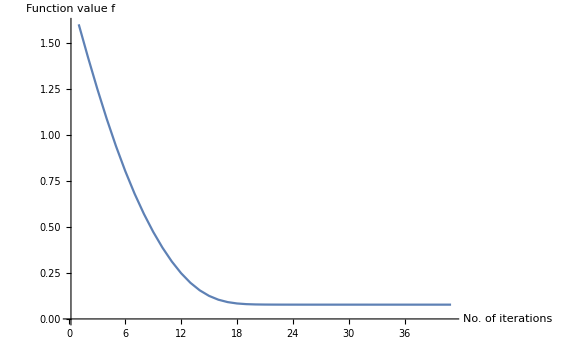

```mathematica
Print["Reason for termination: ",Result[[7]]];
Print["Time taken: ",time," seconds"];
Print["Final value: ",Result⟦1,1⟧];
Print["Number of iterations: ",Length[Result⟦4,1⟧]];
Print["Number of total corrections: ",Result⟦3⟧//Total];
ListPlot[Result⟦5⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All,Joined->True]
```

```mathematica
Mf=Result⟦2,1⟧;
Jfinal=Mf.J0.Inverse[Mf];
```

```mathematica
Jfinal⟦Restriction,Restriction⟧//Eigenvalues//Im
```

{1.02478,-1.02478,1.00289,-1.00289,1.,-1.}

```mathematica
{1.024781736491972,-1.024781736491972,1.002889283587004,-1.002889283587004}
```

{1.02478,-1.02478,1.00289,-1.00289}

## Bosonic Complexity of Purification (CoP)

```mathematica
L=100; (* number of lattice sites *)
l=1.; (* lattice spacing *)
m=.1; (* mass *)
dimA1=1; (* sites of subsystem A1 *)
dimB1=3; (* sites of subsystem B1 *)
d=5; (* distance between subsystem A1 and B1 *)
dimPur=dimA1+dimB1; (* dimensions of the purifying systm*)
```

### Pre-algorithm: Create complex structures and initial transformations

```mathematica
CM0=KGcmRes[{L,l,m},{dimA1,dimB1,d}];
{rlist,MTra}=GOExtractStdFormG[CM0];
JT=GOPurifyStandardJBoson[rlist,dimA2+dimB2,"qpqp"];
JR=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)],"qpqp","qpqp"];

J0=JR;
M0=ArrayFlatten[{{MTra,0},{0,IdentityMatrix[2dimPur]}}]//SparseArray; (* Attention: For complexity, we need to put MTra, because JR transforms inversely to JT!!! *)
```

#### Consistency checks

```mathematica
J0.J0//Eigenvalues (*check J0 to describe pure bosonic state*)
```

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
MTra.CM0.Transpose[MTra]//Chop//MatrixForm (* check correct transformation *)
Cosh[2rlist]
```

(1.46243 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.46243 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.22221 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.22221 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.06604 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.06604 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.00032 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00032)

{1.46243,1.22221,1.06604,1.00032}

```mathematica
MTra.GOinvMSp[MTra]//Chop//MatrixForm (* check symplectic *)
```

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

```mathematica
rrlist={rlist⟦1⟧,rlist⟦2⟧,rlist⟦4⟧,rlist⟦3⟧}
CMback=Inverse[MTra].DiagonalMatrix[Cosh/@Flatten[Table[{2r,2r},{r,rlist}]]].Transpose[Inverse[MTra]];CMback//MatrixForm
CM0-CMback//Chop//MatrixForm
```

{0.464018,0.327439,0.0126183,0.180728}

(1.28101 | -5.65113×10^-16 | -0.00697557 | 2.62811×10^-16 | -0.0048107 | -6.89553×10^-16 | -0.00344953 | 2.76688×10^-16
-4.54064×10^-16 | 1.39418 | -1.98192×10^-16 | 0.247118 | 8.43076×10^-16 | 0.209989 | -6.17562×10^-16 | 0.179771
-0.00697557 | -1.84314×10^-16 | 1.28101 | 1.61676×10^-15 | -0.41982 | 3.55271×10^-15 | -0.0813337 | -1.65146×10^-15
2.62811×10^-16 | 0.247118 | 1.67227×10^-15 | 1.39418 | -3.26128×10^-15 | 0.760649 | 1.22125×10^-15 | 0.554542
-0.0048107 | 8.43076×10^-16 | -0.41982 | -3.26128×10^-15 | 1.28101 | -3.33067×10^-16 | -0.41982 | 2.55351×10^-15
-6.89553×10^-16 | 0.209989 | 3.58047×10^-15 | 0.760649 | -3.33067×10^-16 | 1.39418 | -2.52576×10^-15 | 0.760649
-0.00344953 | -5.62484×10^-16 | -0.0813337 | 1.17267×10^-15 | -0.41982 | -2.55351×10^-15 | 1.28101 | -5.68989×10^-16
2.76905×10^-16 | 0.179771 | -1.70697×10^-15 | 0.554542 | 2.53964×10^-15 | 0.760649 | -6.52256×10^-16 | 1.39418)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### 1. Define the problem-specific input arguments

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
ProblemSpecific={function,gradient};
```

### 2. Define the system-specific input arguments

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];
M0List=Table[MatrixExp[RandomReal[{0,0.7},Length[LieBasis]].LieBasis].M0,{i,10}];
geometry=GOGeometryConst[LieBasis,J0,+1];
newM[m_,s_,x_]:=m.GOapproxExp[s,x];
```

```mathematica
SystemSpecific={J0,M0List,LieBasis,geometry,newM};
```

### 3. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-8; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

### Run the Optimization and evaluate results

```mathematica
{time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

Reason for termination: Function value tolerance reached

Time taken: 0.53125 seconds

Final value: 0.980472

Number of iterations: 7

Number of total corrections: 0

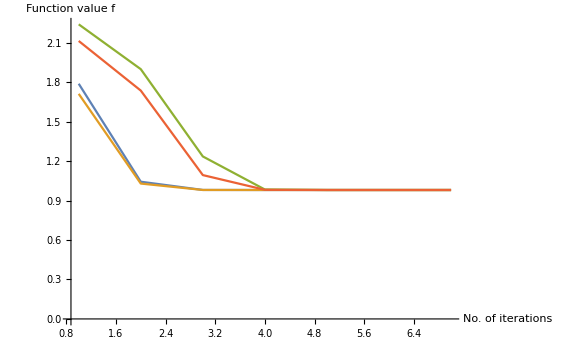

```mathematica
Print["Reason for termination: ",Result[[7]]];
Print["Time taken: ",time," seconds"];
Print["Final value: ",Result⟦1,1⟧];
Print["Number of iterations: ",Length[Result⟦4,1⟧]];
Print["Number of total corrections: ",Result⟦3⟧//Total];
ListPlot[Result⟦5⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All,Joined->True]
```

## Fermionic Entanglement of Purification (EoP)

```mathematica
L=100; (* Total number lattice sites *)
J=1.7;h=1;γ=1; (* XY model parameter*)
dimA1=1; dimB1=3; (* dofs of chosen subystems *)
d=1; (* distance subsystems *)
dimA2=dimA1;dimB2= dimB1; (* purifying dofs, dimA2+dimB2 ≥ dimA1+dimB1 *)
```

### Pre-algorithm: Create complex structures and initial transformations

```mathematica
CM0=XYcmRes[{L,J,h,γ},{dimA1,dimB1,d}];
{rlist,MTra}=GOExtractStdFormΩ[CM0];
J0=GOPurifyStandardJFermion[rlist,dimA2+dimB2,"qpqp"];
M0=ArrayFlatten[{{Inverse[MTra],0},{0,IdentityMatrix[2dimA2+2dimB2]}}]//SparseArray;
```

### 1. Define the problem-specific input arguments

```mathematica
Restriction=GORestrictionAA[{dimA1,dimB1,dimA2,dimB2}];
function=GOEoPFerm[Restriction];
gradient=GOEoPgradFerm[Restriction];

ProblemSpecific={function,gradient};
```

### 2. Define the system-specific input arguments

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSO[dimA2+dimB2]}];
M0List=Table[MatrixExp[RandomReal[{0,0.2},Length[LieBasis]].LieBasis].M0,{i,100}];
```

```mathematica
geometry=GOGeometryConst[LieBasis,J0,-1];
newM[m_,s_,x_]:=m.GOapproxExp[s,x];

SystemSpecific={J0,M0List,LieBasis,geometry,newM};
```

### 3. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-8; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

### Run the Optimization and evaluate results

```mathematica
{time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

Reason for termination: Function value tolerance reached

Time taken: 3.29688 seconds

Final value: 0.100205

Number of iterations: 105

Number of total corrections: 0

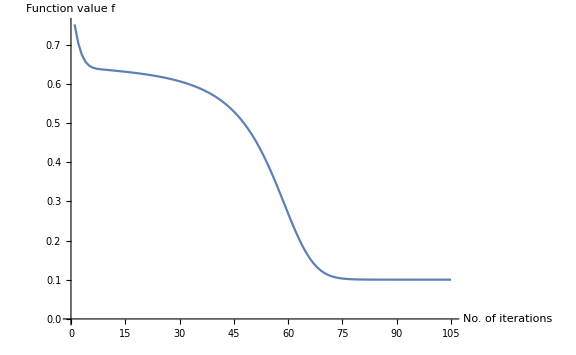

```mathematica
Print["Reason for termination: ",Result[[7]]];
Print["Time taken: ",time," seconds"];
Print["Final value: ",Result⟦1,1⟧];
Print["Number of iterations: ",Length[Result⟦4,1⟧]];
Print["Number of total corrections: ",Result⟦3⟧//Total];
ListPlot[Result⟦5⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All,Joined->True]
```

## Fermionic Complexity of Purification (CoP)

```mathematica
L=100; (* Total number lattice sites *)
J=2.5;h=2;γ=1; (* XY model parameter*)
dimA1=1; dimB1=3; (* dofs of chosen subystems *)
d=5; (* distance subsystems *)
dimPur=dimA1+dimB1; (* dimensions of the purifying system*)
```

### Pre-algorithm: Create complex structures and initial transformations

```mathematica
CM0=XYcmRes[{L,J,h,γ},{dimA1,dimB1,d}];
{rlist,MTra}=GOExtractStdFormΩ[CM0];

JT=GOPurifyStandardJFermion[rlist,dimPur,"qpqp"];
JR=GOTransformΩtoJ[GOΩqpqp[dimA1+dimB1+dimPur],"qpqp","qpqp"]; (* reference state *)

J0=JR;
M0=ArrayFlatten[{{MTra,0},{0,IdentityMatrix[2dimPur]}}]//SparseArray; (* Attention: For complexity, we need to put MTra, because JR transforms inversely to JT!!! *)
```

### 1. Define the problem-specific input arguments

```mathematica
function=GOCoPFerm[JT]; gradient=GOCoPgradFerm[JT];
ProblemSpecific={function,gradient};
```

### 2. Define the system-specific input arguments

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSONoUN[dimPur]}];
M0List=Table[MatrixExp[RandomReal[{0,0.7},Length[LieBasis]].LieBasis].M0,{i,10}];
geometry=GOGeometryConst[LieBasis,J0,-1];
newM[m_,s_,x_]:=m.GOapproxExp[s,x];
```

```mathematica
SystemSpecific={J0,M0List,LieBasis,geometry,newM};
```

### 3. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-8; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

### Run the Optimization and evaluate results

```mathematica
{time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

Reason for termination: Function value tolerance reached

Time taken: 11.2969 seconds

Final value: 1.0434

Number of iterations: 786

Number of total corrections: 0

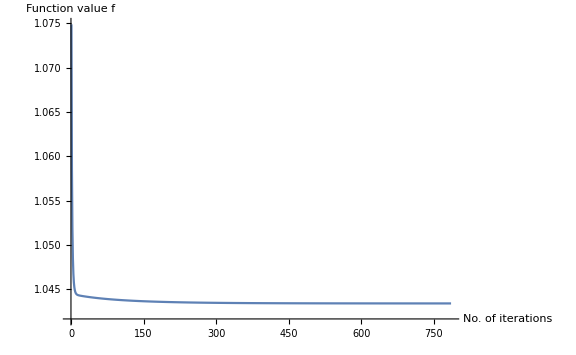

```mathematica
Print["Reason for termination: ",Result[[7]]];
Print["Time taken: ",time," seconds"];
Print["Final value: ",Result⟦1,1⟧];
Print["Number of iterations: ",Length[Result⟦4,1⟧]];
Print["Number of total corrections: ",Result⟦3⟧//Total];
ListPlot[Result⟦5⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All,Joined->True]
```